# bimodal analysis of myelin orientation from 2D histology

- 2D slice of human V1/V2 region
- SMI-94 labeled
- processed by Random Forest classifier trained on foreground (SMI-94 positive structures) using Ilastik
- estimated cortical normals from manually masked (GM/WM, GM/CSF boundaries) image downsampled to 100 micron resolution (corresponding to MR resolution)
- small patches (100 by 100 microns) for analysis of orientation (foreground probability)

## Setup

```mathematica
<<ColorBrewer`
```

```mathematica
DisplayPalettes[SequentialPalettes,8]
```

{{Reds,{RGBColor[1, Rational[49, 51], Rational[16, 17]],RGBColor[Rational[254, 255], Rational[224, 255], Rational[14, 17]],RGBColor[Rational[84, 85], Rational[11, 15], Rational[161, 255]],RGBColor[Rational[84, 85], Rational[146, 255], Rational[38, 85]],RGBColor[Rational[251, 255], Rational[106, 255], Rational[74, 255]],RGBColor[Rational[239, 255], Rational[59, 255], Rational[44, 255]],RGBColor[Rational[203, 255], Rational[8, 85], Rational[29, 255]],RGBColor[Rational[3, 5], 0, Rational[13, 255]]}},{YlOrRd,{RGBColor[1, 1, Rational[4, 5]],RGBColor[1, Rational[79, 85], Rational[32, 51]],RGBColor[Rational[254, 255], Rational[217, 255], Rational[118, 255]],RGBColor[Rational[254, 255], Rational[178, 255], Rational[76, 255]],RGBColor[Rational[253, 255], Rational[47, 85], Rational[4, 17]],RGBColor[Rational[84, 85], Rational[26, 85], Rational[14, 85]],RGBColor[Rational[227, 255], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[59, 85], 0, Rational[38, 255]]}},{RdPu,{RGBColor[1, Rational[247, 255], Rational[81, 85]],RGBColor[Rational[253, 255], Rational[224, 255], Rational[13, 15]],RGBColor[Rational[84, 85], Rational[197, 255], Rational[64, 85]],RGBColor[Rational[50, 51], Rational[53, 85], Rational[181, 255]],RGBColor[Rational[247, 255], Rational[104, 255], Rational[161, 255]],RGBColor[Rational[13, 15], Rational[52, 255], Rational[151, 255]],RGBColor[Rational[58, 85], Rational[1, 255], Rational[42, 85]],RGBColor[Rational[122, 255], Rational[1, 255], Rational[7, 15]]}},{OrRd,{RGBColor[1, Rational[247, 255], Rational[236, 255]],RGBColor[Rational[254, 255], Rational[232, 255], Rational[40, 51]],RGBColor[Rational[253, 255], Rational[212, 255], Rational[158, 255]],RGBColor[Rational[253, 255], Rational[11, 15], Rational[44, 85]],RGBColor[Rational[84, 85], Rational[47, 85], Rational[89, 255]],RGBColor[Rational[239, 255], Rational[101, 255], Rational[24, 85]],RGBColor[Rational[43, 51], Rational[16, 85], Rational[31, 255]],RGBColor[Rational[3, 5], 0, 0]}},{PuBu,{RGBColor[1, Rational[247, 255], Rational[251, 255]],RGBColor[Rational[236, 255], Rational[77, 85], Rational[242, 255]],RGBColor[Rational[208, 255], Rational[209, 255], Rational[46, 51]],RGBColor[Rational[166, 255], Rational[63, 85], Rational[73, 85]],RGBColor[Rational[116, 255], Rational[169, 255], Rational[69, 85]],RGBColor[Rational[18, 85], Rational[48, 85], Rational[64, 85]],RGBColor[Rational[1, 51], Rational[112, 255], Rational[176, 255]],RGBColor[Rational[1, 85], Rational[26, 85], Rational[41, 85]]}},{Greens,{RGBColor[Rational[247, 255], Rational[84, 85], Rational[49, 51]],RGBColor[Rational[229, 255], Rational[49, 51], Rational[224, 255]],RGBColor[Rational[199, 255], Rational[233, 255], Rational[64, 85]],RGBColor[Rational[161, 255], Rational[217, 255], Rational[31, 51]],RGBColor[Rational[116, 255], Rational[196, 255], Rational[118, 255]],RGBColor[Rational[13, 51], Rational[57, 85], Rational[31, 85]],RGBColor[Rational[7, 51], Rational[139, 255], Rational[23, 85]],RGBColor[0, Rational[6, 17], Rational[10, 51]]}},{GnBu,{RGBColor[Rational[247, 255], Rational[84, 85], Rational[16, 17]],RGBColor[Rational[224, 255], Rational[81, 85], Rational[73, 85]],RGBColor[Rational[4, 5], Rational[47, 51], Rational[197, 255]],RGBColor[Rational[56, 85], Rational[13, 15], Rational[181, 255]],RGBColor[Rational[41, 85], Rational[4, 5], Rational[196, 255]],RGBColor[Rational[26, 85], Rational[179, 255], Rational[211, 255]],RGBColor[Rational[43, 255], Rational[28, 51], Rational[38, 51]],RGBColor[Rational[8, 255], Rational[88, 255], Rational[158, 255]]}},{BuPu,{RGBColor[Rational[247, 255], Rational[84, 85], Rational[253, 255]],RGBColor[Rational[224, 255], Rational[236, 255], Rational[244, 255]],RGBColor[Rational[191, 255], Rational[211, 255], Rational[46, 51]],RGBColor[Rational[158, 255], Rational[188, 255], Rational[218, 255]],RGBColor[Rational[28, 51], Rational[10, 17], Rational[66, 85]],RGBColor[Rational[28, 51], Rational[107, 255], Rational[59, 85]],RGBColor[Rational[8, 15], Rational[13, 51], Rational[157, 255]],RGBColor[Rational[22, 51], Rational[1, 255], Rational[107, 255]]}},{Greys,{RGBColor[1, 1, 1],RGBColor[Rational[16, 17], Rational[16, 17], Rational[16, 17]],RGBColor[Rational[217, 255], Rational[217, 255], Rational[217, 255]],RGBColor[Rational[63, 85], Rational[63, 85], Rational[63, 85]],RGBColor[Rational[10, 17], Rational[10, 17], Rational[10, 17]],RGBColor[Rational[23, 51], Rational[23, 51], Rational[23, 51]],RGBColor[Rational[82, 255], Rational[82, 255], Rational[82, 255]],RGBColor[Rational[37, 255], Rational[37, 255], Rational[37, 255]]}},{Oranges,{RGBColor[1, Rational[49, 51], Rational[47, 51]],RGBColor[Rational[254, 255], Rational[46, 51], Rational[206, 255]],RGBColor[Rational[253, 255], Rational[208, 255], Rational[54, 85]],RGBColor[Rational[253, 255], Rational[58, 85], Rational[107, 255]],RGBColor[Rational[253, 255], Rational[47, 85], Rational[4, 17]],RGBColor[Rational[241, 255], Rational[7, 17], Rational[19, 255]],RGBColor[Rational[217, 255], Rational[24, 85], Rational[1, 255]],RGBColor[Rational[28, 51], Rational[3, 17], Rational[4, 255]]}},{YlGnBu,{RGBColor[1, 1, Rational[217, 255]],RGBColor[Rational[79, 85], Rational[248, 255], Rational[59, 85]],RGBColor[Rational[199, 255], Rational[233, 255], Rational[12, 17]],RGBColor[Rational[127, 255], Rational[41, 51], Rational[11, 15]],RGBColor[Rational[13, 51], Rational[182, 255], Rational[196, 255]],RGBColor[Rational[29, 255], Rational[29, 51], Rational[64, 85]],RGBColor[Rational[2, 15], Rational[94, 255], Rational[56, 85]],RGBColor[Rational[4, 85], Rational[44, 255], Rational[44, 85]]}},{BuGn,{RGBColor[Rational[247, 255], Rational[84, 85], Rational[253, 255]],RGBColor[Rational[229, 255], Rational[49, 51], Rational[83, 85]],RGBColor[Rational[4, 5], Rational[236, 255], Rational[46, 51]],RGBColor[Rational[3, 5], Rational[72, 85], Rational[67, 85]],RGBColor[Rational[2, 5], Rational[194, 255], Rational[164, 255]],RGBColor[Rational[13, 51], Rational[58, 85], Rational[118, 255]],RGBColor[Rational[7, 51], Rational[139, 255], Rational[23, 85]],RGBColor[0, Rational[88, 255], Rational[12, 85]]}},{YlOrBr,{RGBColor[1, 1, Rational[229, 255]],RGBColor[1, Rational[247, 255], Rational[188, 255]],RGBColor[Rational[254, 255], Rational[227, 255], Rational[29, 51]],RGBColor[Rational[254, 255], Rational[196, 255], Rational[79, 255]],RGBColor[Rational[254, 255], Rational[3, 5], Rational[41, 255]],RGBColor[Rational[236, 255], Rational[112, 255], Rational[4, 51]],RGBColor[Rational[4, 5], Rational[76, 255], Rational[2, 255]],RGBColor[Rational[28, 51], Rational[3, 17], Rational[4, 255]]}},{PuRd,{RGBColor[Rational[247, 255], Rational[244, 255], Rational[83, 85]],RGBColor[Rational[77, 85], Rational[15, 17], Rational[239, 255]],RGBColor[Rational[212, 255], Rational[37, 51], Rational[218, 255]],RGBColor[Rational[67, 85], Rational[148, 255], Rational[199, 255]],RGBColor[Rational[223, 255], Rational[101, 255], Rational[176, 255]],RGBColor[Rational[77, 85], Rational[41, 255], Rational[46, 85]],RGBColor[Rational[206, 255], Rational[6, 85], Rational[86, 255]],RGBColor[Rational[29, 51], 0, Rational[21, 85]]}},{Blues,{RGBColor[Rational[247, 255], Rational[251, 255], 1],RGBColor[Rational[74, 85], Rational[47, 51], Rational[247, 255]],RGBColor[Rational[66, 85], Rational[73, 85], Rational[239, 255]],RGBColor[Rational[158, 255], Rational[202, 255], Rational[15, 17]],RGBColor[Rational[107, 255], Rational[58, 85], Rational[214, 255]],RGBColor[Rational[22, 85], Rational[146, 255], Rational[66, 85]],RGBColor[Rational[11, 85], Rational[113, 255], Rational[181, 255]],RGBColor[Rational[8, 255], Rational[23, 85], Rational[148, 255]]}},{PuBuGn,{RGBColor[1, Rational[247, 255], Rational[251, 255]],RGBColor[Rational[236, 255], Rational[226, 255], Rational[16, 17]],RGBColor[Rational[208, 255], Rational[209, 255], Rational[46, 51]],RGBColor[Rational[166, 255], Rational[63, 85], Rational[73, 85]],RGBColor[Rational[103, 255], Rational[169, 255], Rational[69, 85]],RGBColor[Rational[18, 85], Rational[48, 85], Rational[64, 85]],RGBColor[Rational[2, 255], Rational[43, 85], Rational[46, 85]],RGBColor[Rational[1, 255], Rational[20, 51], Rational[16, 51]]}},{YlGn,{RGBColor[1, 1, Rational[229, 255]],RGBColor[Rational[247, 255], Rational[84, 85], Rational[37, 51]],RGBColor[Rational[217, 255], Rational[16, 17], Rational[163, 255]],RGBColor[Rational[173, 255], Rational[13, 15], Rational[142, 255]],RGBColor[Rational[8, 17], Rational[66, 85], Rational[121, 255]],RGBColor[Rational[13, 51], Rational[57, 85], Rational[31, 85]],RGBColor[Rational[7, 51], Rational[44, 85], Rational[67, 255]],RGBColor[0, Rational[6, 17], Rational[10, 51]]}},{Purples,{RGBColor[Rational[84, 85], Rational[251, 255], Rational[253, 255]],RGBColor[Rational[239, 255], Rational[79, 85], Rational[49, 51]],RGBColor[Rational[218, 255], Rational[218, 255], Rational[47, 51]],RGBColor[Rational[188, 255], Rational[63, 85], Rational[44, 51]],RGBColor[Rational[158, 255], Rational[154, 255], Rational[40, 51]],RGBColor[Rational[128, 255], Rational[25, 51], Rational[62, 85]],RGBColor[Rational[106, 255], Rational[27, 85], Rational[163, 255]],RGBColor[Rational[74, 255], Rational[4, 51], Rational[134, 255]]}}}

```mathematica
DisplayPalettes[DivergingPalettes,10]
```

{{Spectral,{RGBColor[Rational[158, 255], Rational[1, 255], Rational[22, 85]],RGBColor[Rational[71, 85], Rational[62, 255], Rational[79, 255]],RGBColor[Rational[244, 255], Rational[109, 255], Rational[67, 255]],RGBColor[Rational[253, 255], Rational[58, 85], Rational[97, 255]],RGBColor[Rational[254, 255], Rational[224, 255], Rational[139, 255]],RGBColor[Rational[46, 51], Rational[49, 51], Rational[152, 255]],RGBColor[Rational[57, 85], Rational[13, 15], Rational[164, 255]],RGBColor[Rational[2, 5], Rational[194, 255], Rational[11, 17]],RGBColor[Rational[10, 51], Rational[8, 15], Rational[63, 85]],RGBColor[Rational[94, 255], Rational[79, 255], Rational[54, 85]]}},{RdYlGn,{RGBColor[Rational[11, 17], 0, Rational[38, 255]],RGBColor[Rational[43, 51], Rational[16, 85], Rational[13, 85]],RGBColor[Rational[244, 255], Rational[109, 255], Rational[67, 255]],RGBColor[Rational[253, 255], Rational[58, 85], Rational[97, 255]],RGBColor[Rational[254, 255], Rational[224, 255], Rational[139, 255]],RGBColor[Rational[217, 255], Rational[239, 255], Rational[139, 255]],RGBColor[Rational[166, 255], Rational[217, 255], Rational[106, 255]],RGBColor[Rational[2, 5], Rational[63, 85], Rational[33, 85]],RGBColor[Rational[26, 255], Rational[152, 255], Rational[16, 51]],RGBColor[0, Rational[104, 255], Rational[11, 51]]}},{PRGn,{RGBColor[Rational[64, 255], 0, Rational[5, 17]],RGBColor[Rational[118, 255], Rational[14, 85], Rational[131, 255]],RGBColor[Rational[3, 5], Rational[112, 255], Rational[57, 85]],RGBColor[Rational[194, 255], Rational[11, 17], Rational[69, 85]],RGBColor[Rational[77, 85], Rational[212, 255], Rational[232, 255]],RGBColor[Rational[217, 255], Rational[16, 17], Rational[211, 255]],RGBColor[Rational[166, 255], Rational[73, 85], Rational[32, 51]],RGBColor[Rational[6, 17], Rational[58, 85], Rational[97, 255]],RGBColor[Rational[9, 85], Rational[8, 17], Rational[11, 51]],RGBColor[0, Rational[4, 15], Rational[9, 85]]}},{RdBu,{RGBColor[Rational[103, 255], 0, Rational[31, 255]],RGBColor[Rational[178, 255], Rational[8, 85], Rational[43, 255]],RGBColor[Rational[214, 255], Rational[32, 85], Rational[77, 255]],RGBColor[Rational[244, 255], Rational[11, 17], Rational[26, 51]],RGBColor[Rational[253, 255], Rational[73, 85], Rational[199, 255]],RGBColor[Rational[209, 255], Rational[229, 255], Rational[16, 17]],RGBColor[Rational[146, 255], Rational[197, 255], Rational[74, 85]],RGBColor[Rational[67, 255], Rational[49, 85], Rational[13, 17]],RGBColor[Rational[11, 85], Rational[2, 5], Rational[172, 255]],RGBColor[Rational[1, 51], Rational[16, 85], Rational[97, 255]]}},{RdGy,{RGBColor[Rational[103, 255], 0, Rational[31, 255]],RGBColor[Rational[178, 255], Rational[8, 85], Rational[43, 255]],RGBColor[Rational[214, 255], Rational[32, 85], Rational[77, 255]],RGBColor[Rational[244, 255], Rational[11, 17], Rational[26, 51]],RGBColor[Rational[253, 255], Rational[73, 85], Rational[199, 255]],RGBColor[Rational[224, 255], Rational[224, 255], Rational[224, 255]],RGBColor[Rational[62, 85], Rational[62, 85], Rational[62, 85]],RGBColor[Rational[9, 17], Rational[9, 17], Rational[9, 17]],RGBColor[Rational[77, 255], Rational[77, 255], Rational[77, 255]],RGBColor[Rational[26, 255], Rational[26, 255], Rational[26, 255]]}},{RdYlBu,{RGBColor[Rational[11, 17], 0, Rational[38, 255]],RGBColor[Rational[43, 51], Rational[16, 85], Rational[13, 85]],RGBColor[Rational[244, 255], Rational[109, 255], Rational[67, 255]],RGBColor[Rational[253, 255], Rational[58, 85], Rational[97, 255]],RGBColor[Rational[254, 255], Rational[224, 255], Rational[48, 85]],RGBColor[Rational[224, 255], Rational[81, 85], Rational[248, 255]],RGBColor[Rational[57, 85], Rational[217, 255], Rational[233, 255]],RGBColor[Rational[116, 255], Rational[173, 255], Rational[209, 255]],RGBColor[Rational[23, 85], Rational[39, 85], Rational[12, 17]],RGBColor[Rational[49, 255], Rational[18, 85], Rational[149, 255]]}},{PiYG,{RGBColor[Rational[142, 255], Rational[1, 255], Rational[82, 255]],RGBColor[Rational[197, 255], Rational[9, 85], Rational[25, 51]],RGBColor[Rational[74, 85], Rational[7, 15], Rational[58, 85]],RGBColor[Rational[241, 255], Rational[182, 255], Rational[218, 255]],RGBColor[Rational[253, 255], Rational[224, 255], Rational[239, 255]],RGBColor[Rational[46, 51], Rational[49, 51], Rational[208, 255]],RGBColor[Rational[184, 255], Rational[15, 17], Rational[134, 255]],RGBColor[Rational[127, 255], Rational[188, 255], Rational[13, 51]],RGBColor[Rational[77, 255], Rational[146, 255], Rational[11, 85]],RGBColor[Rational[13, 85], Rational[20, 51], Rational[5, 51]]}},{PuOr,{RGBColor[Rational[127, 255], Rational[59, 255], Rational[8, 255]],RGBColor[Rational[179, 255], Rational[88, 255], Rational[2, 85]],RGBColor[Rational[224, 255], Rational[26, 51], Rational[4, 51]],RGBColor[Rational[253, 255], Rational[184, 255], Rational[33, 85]],RGBColor[Rational[254, 255], Rational[224, 255], Rational[182, 255]],RGBColor[Rational[72, 85], Rational[218, 255], Rational[47, 51]],RGBColor[Rational[178, 255], Rational[57, 85], Rational[14, 17]],RGBColor[Rational[128, 255], Rational[23, 51], Rational[172, 255]],RGBColor[Rational[28, 85], Rational[13, 85], Rational[8, 15]],RGBColor[Rational[3, 17], 0, Rational[5, 17]]}},{BrBG,{RGBColor[Rational[28, 85], Rational[16, 85], Rational[1, 51]],RGBColor[Rational[28, 51], Rational[27, 85], Rational[2, 51]],RGBColor[Rational[191, 255], Rational[43, 85], Rational[3, 17]],RGBColor[Rational[223, 255], Rational[194, 255], Rational[25, 51]],RGBColor[Rational[82, 85], Rational[232, 255], Rational[13, 17]],RGBColor[Rational[199, 255], Rational[78, 85], Rational[229, 255]],RGBColor[Rational[128, 255], Rational[41, 51], Rational[193, 255]],RGBColor[Rational[53, 255], Rational[151, 255], Rational[143, 255]],RGBColor[Rational[1, 255], Rational[2, 5], Rational[94, 255]],RGBColor[0, Rational[4, 17], Rational[16, 85]]}}}

```mathematica
rainbow=CreateColorFunction[Spectral,11];
```

```mathematica
palette=CreateColorFunction[RdBu,11];
```

```mathematica
palettePRGn=CreateColorFunction[PRGn,11];
```

```mathematica
palettePiYG=CreateColorFunction[PiYG,11];
reds=CreateColorFunction[Reds,8];
greys=CreateColorFunction[Greys,8];
blues=CreateColorFunction[Blues,8];
```

```mathematica
blues[0.4]
```

RGBColor[0.6509803921568627, 0.8054901960784313, 0.8933333333333333]

```mathematica
srcdir=NotebookDirectory[]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/src/

```mathematica
root=FileNameJoin[Most[FileNameSplit[NotebookDirectory[]]]]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D

```mathematica
datadir=FileNameJoin[Append[FileNameSplit[root],"data"]]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/data

```mathematica
resdir=FileNameJoin[Append[FileNameSplit[root],"results"]]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results

```mathematica
mask=Import[FileNameJoin[Append[FileNameSplit[datadir],"cortex-mask_1.png"]]];
```

```mathematica
mask=Binarize[mask]
```

-Graphics-

```mathematica
orientationNormals=Import[FileNameJoin[Append[FileNameSplit[datadir],"estimated-cortical-normals-x-y-z-2.0.tif"]]];
```

```mathematica
ImageDimensions[orientationNormals[[1]]]
```

{188,239}

```mathematica
Dimensions[ImageData[orientationNormals[[1]]]]
```

{239,188}

Last voxel coordinates from plugin are 187, 238. Thus, the name of the voxel file should correspond to the image (data) coordinates of the orientation normals in the following way: test-133-116.tif is the value at imagedata[[ 117,134]].

```mathematica
xyOrientation={ImageData[orientationNormals[[1]]],ImageData[orientationNormals[[2]]]};
```

```mathematica
voxels=FileNames[{"*"},datadir<>"/voxels-clj-plugin/"];
```

```mathematica
gmVoxels=Position[ImageData[mask],1];
```

```mathematica
gmVoxels;
```

## orientation analysis

functions

```mathematica
Clear[coordsFromName]
coordsFromName[filename_]:=Rest[Most[StringSplit[Last[StringSplit[filename,"/"]],{"-","."}]]]
```

```mathematica
Clear[coordsToName]
coordsToName[{x_,y_},prefix_:"voxels-clj-plugin"]:=FileNameJoin[{datadir,prefix,"test-"<>ToString[y]<>"-"<>ToString[x]<>".tif"}]
```

```mathematica
Clear[coordsToOutputName]
coordsToOutputName[{x_,y_},prefix_:"orientation-samples",suffix_:".csv"]:=FileNameJoin[{resdir,prefix,"test-"<>ToString[y]<>"-"<>ToString[x]<>suffix}]
```

```mathematica
Clear[getOrientation]
getOrientation[{x_,y_}]:=If[xyOrientation[[1,x,y]]≠ 0 , ArcTan[-xyOrientation[[2,x,y]]/xyOrientation[[1,x,y]]],0]
```

```mathematica
colorCodeOrientation[gradX_,gradY_]:=Module[
{nx,ny},
{nx,ny}=Dimensions[gradX];
Table[getOrientation[x,y],{x,1,nx},{y,1,ny}]
]
```

```mathematica
Clear[angleToOrientation]
angleToOrientation[angle_,scale_:10]:={25,25}+scale*{-{Cos[angle],Sin[angle]},{Cos[angle],Sin[angle]}}
```

```mathematica
Clear[fitBimodalVonMises]
fitBimodalVonMises[{x_,y_},sigma_:2,nBins_:16]:=Module[
{pimg,o,w,A,hist,estDist,mse},
pimg=Import[coordsToName[{x,y}]];
o = Flatten[ImageData[GradientOrientationFilter[pimg,sigma]]];
w = Flatten[ImageData[GradientFilter[pimg,sigma]]];
If[Total[w]<$MachineEpsilon,Return[-1]];
A = WeightedData[o,w];
hist=HistogramDistribution[A,nBins];
estDist=EstimatedDistribution[A,MixtureDistribution[{w1,w2},{VonMisesDistribution[m1,k1],VonMisesDistribution[m2,k2]}]];
mse=Total[Table[(PDF[hist,i]-PDF[estDist,i])^2,{i,-π/2,π/2,π/16}]]/16;

{ImageAdjust[pimg],Show[Plot[PDF[hist,t],{t,-π/2, π/2},Filling->Axis, PlotRange->All],Plot[PDF[estDist,t],{t,-π/2,π/2}]],getOrientation[{x,y}],mse,estDist[[1]],{estDist[[2,1,1]],estDist[[2,2,1]]},Total[w]}

]
```

```mathematica
Clear[analyzeOrientation]
analyzeOrientation[{x_,y_},sigma_:2,nBins_:16]:=Module[
{pimg,o,w,A,hist,estDist,mse,corticalNormal,spread,means,dist2corticalNormal,normalComponent,mixtureWeights},
pimg=Import[coordsToName[{x,y}]];
o = Flatten[ImageData[GradientOrientationFilter[pimg,sigma]]];
w = Flatten[ImageData[GradientFilter[pimg,sigma]]];
If[Total[w]<$MachineEpsilon,Return[-1]];
A = WeightedData[o,w];
hist=HistogramDistribution[A,nBins];
estDist=EstimatedDistribution[A,MixtureDistribution[{w1,w2},{VonMisesDistribution[m1,k1],VonMisesDistribution[m2,k2]}]];
mse=Total[Table[(PDF[hist,i]-PDF[estDist,i])^2,{i,-π/2,π/2,π/16}]]/16;
corticalNormal=getOrientation[{x,y}];
means={estDist[[2,1,1]],estDist[[2,2,1]]};
spread={estDist[[2,1,2]],estDist[[2,2,2]]};
dist2corticalNormal=Abs[#-corticalNormal]&/@means;
normalComponent=Position[dist2corticalNormal,Min[dist2corticalNormal]][[1,1]];
mixtureWeights=estDist[[1]];
Flatten[{x,y,Flatten[{mixtureWeights[[normalComponent]],Complement[mixtureWeights,{mixtureWeights[[normalComponent]]}]}],mse,Flatten[{corticalNormal,means[[normalComponent]],Complement[means,{means[[normalComponent]]}]}],Flatten[{spread[[normalComponent]],Complement[spread,{means[[normalComponent]]}]}]}]
]
```

```mathematica
Clear[estimateFibreDensity]
estimateFibreDensity[coords_]:=Module[
{imgdata},
imgdata=Flatten[ImageData[Import[coordsToName[coords]]]];
Total[imgdata]/Length[imgdata]
]
```

run analysis

## fibre density

```mathematica
gmVoxels[[1]]
```

{32,96}

```mathematica
imgdata=Flatten[ImageData[Import[coordsToName[gmVoxels[[1]]]]]];
```

```mathematica
Total[imgdata]/Length[imgdata]
```

0.566304

```mathematica
headerDensity={"x","y","density"};
```

```mathematica
densities={Sequence@@#,estimateFibreDensity[#]}&/@gmVoxels;
```

```mathematica
Export[FileNameJoin[{root,"results","fibre-densities.csv"}],Prepend[densities,headerDensity]]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/fibre-densities.csv

```mathematica
TableForm[Take[densities,20]]
```

31 | 94 | 0.606938
31 | 95 | 0.63538
31 | 96 | 0.590155
31 | 97 | 0.528461
31 | 98 | 0.5357
31 | 99 | 0.532852
31 | 100 | 0.529622
31 | 101 | 0.484827
31 | 102 | 0.485222
31 | 103 | 0.492013
31 | 104 | 0.392878
31 | 105 | 0.238481
31 | 106 | 0.151346
31 | 107 | 0.0158232
32 | 94 | 0.588039
32 | 95 | 0.666811
32 | 96 | 0.566304
32 | 97 | 0.46499
32 | 98 | 0.447762
32 | 99 | 0.490827

## orientation distribution

```mathematica
header={"x","y","weight normal","weight parallel", "mse", "normal angle", "normal component angle", "parallel component angle","normal component spread", "parallel component spread"}
```

{x,y,weight normal,weight parallel,mse,normal angle,normal component angle,parallel component angle,normal component spread,parallel component spread}

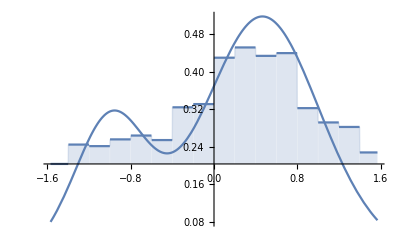
{-Graphics-,-Graphics-,-1.52909,0.00601095,{0.253819,0.746181},{-0.996876,0.465846},348.086}

```mathematica
fitBimodalVonMises[gmVoxels[[400]]]
```

```mathematica
range=Max[w]-Min[w]
```

0

```mathematica
max=Max[w]
```

0.367635

```mathematica
min=Min[w]
```

0.0000462222

```mathematica
repeats=Round[1((#-min)/range)]&/@w;
```

```mathematica
samples=Flatten[ConstantArray[#[[1]],#[[2]]]&/@Transpose[{o,repeats}]];
```

```mathematica
Clear[extractOrientations]
extractOrientations[{x_,y_}]:=Module[
{pimg,o,w,repeats,samples,range,min,vecs},
pimg=Import[coordsToName[{x,y}]];
o = Flatten[ImageData[GradientOrientationFilter[pimg,2]]];
w = Flatten[ImageData[GradientFilter[pimg,2]]];
If[Total[w]<$MachineEpsilon,Return[-1]];
range=Max[w]-Min[w];
min=Min[w];
repeats=Round[1((#-min)/range)]&/@w;
samples=Flatten[ConstantArray[#[[1]],#[[2]]]&/@Transpose[{o,repeats}]];
vecs={Cos[#],Sin[#]}&/@samples;
Export[coordsToOutputName[{x,y}],vecs]
]
```

```mathematica
extractOrientations/@gmVoxels
```

{/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientation-samples/test-96-32.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientation-samples/test-97-32.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientation-samples/test-98-32.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientation-samples/test-99-32.csv,13944,-1,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientation-samples/test-120-221.csv,-1,-1}
 |  |  |  |

```mathematica
coordsToOutputName[{20,10}]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientation-samples/test-10-20.csv

```mathematica
coordsToName[{20,10}]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/data/voxels-clj-plugin/test-10-20.tif

```mathematica
pimg=Import[coordsToName[gmVoxels[[400]]]];
o = Flatten[ImageData[GradientOrientationFilter[pimg,2]]];
w = Flatten[ImageData[GradientFilter[pimg,2]]];
If[Total[w]<$MachineEpsilon,Return[-1]];
A = WeightedData[o,w];
```

```mathematica
vecs={Cos[#],Sin[#]}&/@o
```

{{0.755705,0.654912},{0.372967,0.927845},{0.577161,0.816631},{0.596302,0.80276},{0.77504,0.631912},{0.790107,0.612969},2488,{0.678962,0.734173},{0.562217,0.82699},{0.61972,0.784823},{0.972131,-0.234438},{0.173323,-0.984865},{0.0336268,0.999434}}
 |  |  |  |

```mathematica
Export["~/Desktop/orientation.csv",vecs]
```

~/Desktop/orientation.csv

WeightedData::invprp: The argument 1 is not a valid property. Specify "Properties" to obtain a list of valid properties.

WeightedData[…][1]

```mathematica
Clear[computeBatch]
computeBatch[k_]:=Module[
{orientations},
orientations=Table[analyzeOrientation[gmVoxels[[i]]],{i,(k-1)100 + 1,k 100}];
Export[FileNameJoin[{root,"results","orientations-2.0","orientations-batch"<>IntegerString[k,10,5]<>".csv"}],Prepend[orientations,header]]
]
```

```mathematica
Table[computeBatch[t],{t,5,20}]
```

```mathematica
Length[gmVoxels]
```

13692

```mathematica
Last[gmVoxels]
```

{216,125}

```mathematica
136*100
```

13600

```mathematica
Clear[computeLastBatch]
computeLastBatch[]:=Module[
{orientations},
orientations=Table[analyzeOrientation[gmVoxels[[i]]],{i,13601,13692}];
Export[FileNameJoin[{root,"results","orientations-batch"<>IntegerString[137,10,5]<>".csv"}],Prepend[orientations,header]]
]
```

```mathematica
computeLastBatch[]
```

General::munfl: 1.09286×10^-278 6.42535×10^-279 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.14902×10^-268 6.42535×10^-279 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.72875×10^-247 6.42535×10^-279 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00137.csv

```mathematica
Table[computeBatch[t],{t,131,200}]
```

General::munfl: 1.09286×10^-278 6.42535×10^-279 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.14902×10^-268 6.42535×10^-279 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.72875×10^-247 6.42535×10^-279 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Part::partw: Part 13693 of {{31,94},{31,95},{31,96},{31,97},{31,98},{31,99},{31,100},{31,101},{31,102},{31,103},{31,104},{31,105},{31,106},{31,107},{32,94},{32,95},{32,96},{32,97},«15»,{33,96},{33,97},{33,98},{33,99},{33,100},{33,101},{33,102},{33,103},{33,104},{33,105},{33,106},{33,107},{33,108},{33,109},{33,110},{33,111},{33,112},«13642»} does not exist.

Part::partw: Part 13694 of {{31,94},{31,95},{31,96},{31,97},{31,98},{31,99},{31,100},{31,101},{31,102},{31,103},{31,104},{31,105},{31,106},{31,107},{32,94},{32,95},{32,96},{32,97},«15»,{33,96},{33,97},{33,98},{33,99},{33,100},{33,101},{33,102},{33,103},{33,104},{33,105},{33,106},{33,107},{33,108},{33,109},{33,110},{33,111},{33,112},«13642»} does not exist.

Part::partw: Part 13695 of {{31,94},{31,95},{31,96},{31,97},{31,98},{31,99},{31,100},{31,101},{31,102},{31,103},{31,104},{31,105},{31,106},{31,107},{32,94},{32,95},{32,96},{32,97},«15»,{33,96},{33,97},{33,98},{33,99},{33,100},{33,101},{33,102},{33,103},{33,104},{33,105},{33,106},{33,107},{33,108},{33,109},{33,110},{33,111},{33,112},«13642»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00131.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00132.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00133.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00134.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00135.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00136.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00137.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00138.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00139.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00140.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00141.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00142.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00143.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00144.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00145.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00146.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00147.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00148.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00149.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00150.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00151.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00152.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00153.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00154.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00155.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00156.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00157.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00158.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00159.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00160.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00161.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00162.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00163.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00164.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00165.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00166.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00167.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00168.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00169.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00170.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00171.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00172.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00173.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00174.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00175.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00176.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00177.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00178.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00179.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00180.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00181.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00182.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00183.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00184.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00185.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00186.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00187.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00188.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00189.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00190.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00191.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00192.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00193.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00194.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00195.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00196.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00197.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00198.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00199.csv,/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00200.csv}

```mathematica
missing={80,}
```

```mathematica
Table[computeBatch[t],{t,51,300}]
```

```mathematica
k = 2;
orientations=Table[analyzeOrientation[gmVoxels[[i]]],{i,101,200}];
Export[FileNameJoin[{root,"results","orientations-batch"<>IntegerString[k,10,5]<>".csv"}],Prepend[orientations,header]]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00002.csv

```mathematica
k = 6;
orientations=Table[analyzeOrientation[gmVoxels[[i]]],{i,(k-1)100 + 1,k 100}];
Export[FileNameJoin[{root,"results","orientations-batch"<>IntegerString[k,10,5]<>".csv"}],Prepend[orientations,header]]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientations-batch00006.csv

```mathematica
Table[
orientations=Table[analyzeOrientation[gmVoxels[[i]]],{i,(k-1)100 + 1,k 100}];
Export[FileNameJoin[{root,"results","orientations-batch"<>IntegerString[k,10,5]<>".csv"}],Prepend[orientations,header]],{k,4,10}]
```

```mathematica
Length[gmVoxels]
```

13692

```mathematica
Table[
Export[FileNameJoin[{root,"results","orientations-batch"<>IntegerString[i,10,5]<>".csv"}],Prepend[analyzeOrientation/@gmVoxels[[i;;i+100]],header]],
{i,1,Length[gmVoxels]-100,100}
]
```

```mathematica
gmVoxels[[1;;1+100]]
```

{{31,94},{31,95},{31,96},{31,97},{31,98},{31,99},{31,100},{31,101},{31,102},{31,103},{31,104},{31,105},{31,106},{31,107},{32,94},{32,95},{32,96},{32,97},{32,98},{32,99},{32,100},{32,101},{32,102},{32,103},{32,104},{32,105},{32,106},{32,107},{32,108},{32,109},{32,110},{33,94},{33,95},{33,96},{33,97},{33,98},{33,99},{33,100},{33,101},{33,102},{33,103},{33,104},{33,105},{33,106},{33,107},{33,108},{33,109},{33,110},{33,111},{33,112},{34,94},{34,95},{34,96},{34,97},{34,98},{34,99},{34,100},{34,101},{34,102},{34,103},{34,104},{34,105},{34,106},{34,107},{34,108},{34,109},{34,110},{34,111},{34,112},{34,113},{34,114},{34,115},{35,94},{35,95},{35,96},{35,97},{35,98},{35,99},{35,100},{35,101},{35,102},{35,103},{35,104},{35,105},{35,106},{35,107},{35,108},{35,109},{35,110},{35,111},{35,112},{35,113},{35,114},{35,115},{35,116},{35,117},{35,118},{36,94},{36,95},{36,96},{36,97}}

```mathematica
analyzeOrientation[gmVoxels[[101]]]
```

{36,97,0.442077,0.557923,0.0119866,0.456307,0.873515,-0.655223,5.1581,3.45903,5.1581}

```mathematica
gmOrientations=analyzeOrientation/@gmVoxels;
```

```mathematica
Export[FileNameJoin[{root,"results","orientations.csv"}],Prepend[gmOrientations,header]]
```

```mathematica
testVoxels=RandomSample[gmVoxels,25];
```

```mathematica
Prepend[analyzeOrientation[#]&/@testVoxels,header]
```

```mathematica
100 * 2.5 / 60.
```

4.16667

## combine results

```mathematica
csvfiles=FileNames[{"*.csv"},FileNameJoin[{root,"results","orientation"}]];
```

```mathematica
first=Import[csvfiles[[1]]];
```

```mathematica
rest=Rest[Import[#]]&/@Rest[csvfiles];
```

```mathematica
orientationData=Join@@Prepend[rest,first];
```

```mathematica
headerDensity
```

{x,y,density}

```mathematica
header=orientationData[[1]]
```

{x,y,weight normal,weight parallel,mse,normal angle,normal component angle,parallel component angle,normal component spread,parallel component spread,}

```mathematica
combinedHeader=Append[header,"fibre density"]
```

{x,y,weight normal,weight parallel,mse,normal angle,normal component angle,parallel component angle,normal component spread,parallel component spread,,fibre density}

```mathematica
Length[combinedHeader]
```

12

```mathematica
Length[orientationData[[2]]]
```

11

```mathematica
Length[densities]
```

13692

```mathematica
Length[Rest[orientationData]]
```

13692

```mathematica
combinedResult=MapThread[Append[#1,Last[#2]]&,{Rest[orientationData],densities}];
```

```mathematica
res=Prepend[combinedResult,combinedHeader];
```

```mathematica
TableForm[res[[1;;10]]]
```

x | y | weight normal | weight parallel | mse | normal angle | normal component angle | parallel component angle | normal component spread | parallel component spread |  | fibre density
31 | 94 | 0.412882 | 0.587118 | 0.0101853 | -0.695043 | -0.794896 | 0.820066 | 4.60511 | 4.60511 | 5.21961 | 0.606938
31 | 95 | 0.380224 | 0.619776 | 0.00853272 | -1.00388 | -0.822405 | 0.639637 | 4.93911 | 4.06715 | 4.93911 | 0.63538
31 | 96 | 0.395403 | 0.604597 | 0.00937991 | -1.54519 | -0.623041 | 0.852434 | 3.19492 | 3.19492 | 6.55737 | 0.590155
31 | 97 | 0.161312 | 0.838688 | 0.00900637 | -1.5632 | -1.16476 | 0.529254 | 13.1181 | 3.49276 | 13.1181 | 0.528461
31 | 98 | 0.33428 | 0.66572 | 0.015841 | -1.26583 | -0.911851 | 0.808566 | 5.21953 | 4.56619 | 5.21953 | 0.5357
31 | 99 | 0.266265 | 0.733735 | 0.0092471 | -0.429428 | -1.04435 | 0.502154 | 8.25081 | 3.20016 | 8.25081 | 0.532852
31 | 100 | 0.464125 | 0.535875 | 0.0089709 | 0.763743 | 0.980455 | -0.487333 | 9.0838 | 2.94685 | 9.0838 | 0.529622
31 | 101 | 0.462897 | 0.537103 | 0.0106009 | 1.0683 | 0.862324 | -0.705094 | 5.11101 | 3.86123 | 5.11101 | 0.484827
31 | 102 | 0.428085 | 0.571915 | 0.00888184 | 1.03514 | 0.909558 | -0.56912 | 6.2573 | 3.46997 | 6.2573 | 0.485222

```mathematica
firstColumns=Take[#,9]&/@res;
```

```mathematica
lastColumn=Last/@res;
```

```mathematica
spreads=#[[9;;11]]&/@res;
```

```mathematica
spreads[[1;;10]]
```

{{normal component spread,parallel component spread,},{4.60511,4.60511,5.21961},{4.93911,4.06715,4.93911},{3.19492,3.19492,6.55737},{13.1181,3.49276,13.1181},{5.21953,4.56619,5.21953},{8.25081,3.20016,8.25081},{9.0838,2.94685,9.0838},{5.11101,3.86123,5.11101},{6.2573,3.46997,6.2573}}

```mathematica
correctedSpreads=Complement[Rest[#],{First[#]}]&/@spreads[[2;;]];
```

```mathematica
correctedSpreads=Flatten[correctedSpreads];
```

```mathematica
correctedSpreads=Prepend[correctedSpreads,"parallel component spread"];
```

```mathematica
tmp=Join@@#&/@Transpose[{firstColumns,List/@correctedSpreads}];
```

```mathematica
correctedResult=Join@@#&/@Transpose[{tmp,List/@lastColumn}];
```

```mathematica
TableForm[correctedResult[[1;;10]]]
```

x | y | weight normal | weight parallel | mse | normal angle | normal component angle | parallel component angle | normal component spread | parallel component spread | fibre density
31 | 94 | 0.412882 | 0.587118 | 0.0101853 | -0.695043 | -0.794896 | 0.820066 | 4.60511 | 5.21961 | 0.606938
31 | 95 | 0.380224 | 0.619776 | 0.00853272 | -1.00388 | -0.822405 | 0.639637 | 4.93911 | 4.06715 | 0.63538
31 | 96 | 0.395403 | 0.604597 | 0.00937991 | -1.54519 | -0.623041 | 0.852434 | 3.19492 | 6.55737 | 0.590155
31 | 97 | 0.161312 | 0.838688 | 0.00900637 | -1.5632 | -1.16476 | 0.529254 | 13.1181 | 3.49276 | 0.528461
31 | 98 | 0.33428 | 0.66572 | 0.015841 | -1.26583 | -0.911851 | 0.808566 | 5.21953 | 4.56619 | 0.5357
31 | 99 | 0.266265 | 0.733735 | 0.0092471 | -0.429428 | -1.04435 | 0.502154 | 8.25081 | 3.20016 | 0.532852
31 | 100 | 0.464125 | 0.535875 | 0.0089709 | 0.763743 | 0.980455 | -0.487333 | 9.0838 | 2.94685 | 0.529622
31 | 101 | 0.462897 | 0.537103 | 0.0106009 | 1.0683 | 0.862324 | -0.705094 | 5.11101 | 3.86123 | 0.484827
31 | 102 | 0.428085 | 0.571915 | 0.00888184 | 1.03514 | 0.909558 | -0.56912 | 6.2573 | 3.46997 | 0.485222

```mathematica
Export[FileNameJoin[{root,"results","fibre-properties.csv"}],correctedResult]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/fibre-properties.csv

## visualization of results

```mathematica
Clear[coordsToCSV]
coordsToCSV[{x_,y_},prefix_:"voxels-clj-plugin"]:=FileNameJoin[{"/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/orientation-samples/","test-"<>ToString[y]<>"-"<>ToString[x]<>".csv"}]
```

```mathematica
csvfilesFromR=FileNames[{"*.csv"},FileNameJoin[{root,"results","orientation-samples"}]];
```

```mathematica
res=Rest[Import[coordsToCSV[gmVoxels[[200]]]]];
```

```mathematica
Clear[vec2angle]
vec2angle[{x_,y_}]:=If[x≠ 0 , ArcTan[y/x],0]
```

```mathematica
Clear[analyzeVoxel]
analyzeVoxel[{x_,y_}]:=Module[
{clusteredVectors,angles,means,normal,angleDist,ref,vecAngles,radialID,tangentialID},
clusteredVectors=Rest[Import[coordsToCSV[{x,y}]]];
means={Mean[Most/@Select[clusteredVectors,Last[#]==1&]],Mean[Most/@Select[clusteredVectors,Last[#]==2&]]};
(*angles=vec2angle/@means;*)
normal=getOrientation[{x,y}];
ref={Cos[normal],Sin[normal]};
vecAngles={VectorAngle[#,ref]&/@means,VectorAngle[#,-ref]&/@means};
(*radialID=2- Mod[Position[Ordering[Flatten[vecAngles]],1][[1,1]],2];*)
radialID=2- Mod[Position[Flatten[vecAngles],Min[Flatten[vecAngles]]][[1,1]],2];
tangentialID=Complement[{1,2},{radialID}][[1]];
(*angleDist=Abs[#-normal]&/@angles;*)
{Count[Last/@clusteredVectors,radialID],Count[Last/@clusteredVectors,tangentialID],means[[radialID]],means[[tangentialID]],ref,{x,y},Min[Flatten[vecAngles]],radialID}
]
```

```mathematica
fibreFractions=analyzeVoxel/@gmVoxels;
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression 2-Mod[{}⟦1,1⟧,2] cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression 2-Mod[{}⟦1,1⟧,2] cannot be used as a part specification.

Import::nffil: File not found during Import.

Rest::normal: Nonatomic expression expected at position 1 in Rest[$Failed].

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

Rest::argx: Rest called with 0 arguments; 1 argument is expected.

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

Rest::argx: Rest called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Last::argt: Last called with 0 arguments; 1 or 2 arguments are expected.

Part::pkspec1: The expression 2-Mod[{}⟦1,1⟧,2] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Import::nffil: File not found during Import.

Rest::normal: Nonatomic expression expected at position 1 in Rest[$Failed].

Rest::argx: Rest called with 0 arguments; 1 argument is expected.

General::stop: Further output of Rest::argx will be suppressed during this calculation.

Last::argt: Last called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Last::argt will be suppressed during this calculation.

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[$Failed].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

```mathematica
fibreFractionsClean=Select[fibreFractions,And@@(NumericQ/@Flatten[#])&];
```

```mathematica
fibreFractionsClean[[1]]
```

{195,369,{0.708039,-0.589366},{0.733676,0.538038},{0.679744,-0.73345},{32,96},0.1292,2}

```mathematica
Export["/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/fibre-fractions.csv",Flatten/@fibreFractionsClean]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/fibre-fractions.csv

```mathematica
g={Green,Line[{-#[[3]]+{#[[6]][[2]],500-#[[6]][[1]]},#[[3]]+{#[[6]][[2]],500-#[[6]][[1]]}}],Red,Line[{-#[[4]]+{#[[6]][[2]],500-#[[6]][[1]]},#[[4]]+{#[[6]][[2]],500-#[[6]][[1]]}}],Black,Line[{-#[[5]]+{#[[6]][[2]],500-#[[6]][[1]]},#[[5]]+{#[[6]][[2]],500-#[[6]][[1]]}}]}&/@fibreFractionsClean;
```

```mathematica
Graphics[{White,Line[{{#[[2]],500-#[[1]]}-{Cos[getOrientation[#]],Sin[getOrientation[#]]},{#[[2]],500-#[[1]]}+{Cos[getOrientation[#]],Sin[getOrientation[#]]}}]&/@RandomSample[gmVoxels,5000]}]
```

```mathematica
Graphics[RandomSample[g,2000]]
```

```mathematica
Graphics[{reds[(#[[2]]/(#[[1]]+#[[2]]))],Disk[#[[6]],0.5]}&/@fibreFractionsClean,Background->Black]
```

```mathematica
fibreFractionsClean[[1]]
```

{195,369,{0.708039,-0.589366},{0.733676,0.538038},{0.679744,-0.73345},{32,96},0.1292,2}

```mathematica
densityLUT=Most[#]->Last[#]&/@densities;
```

```mathematica
Graphics[{reds[1-(Last[#]/0.35)],Disk[Most[#],0.5]}&/@positionAndValue,Background->Black]
```

```mathematica
fibreFractionsClean=Import["/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/fibre-fractions.csv"];
```

```mathematica
densities=Import["/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/results/densities/fibre-densities.csv"];
```

```mathematica
Dimensions[fibreFractionsClean]
```

{13769,12}

```mathematica
Dimensions[densities]
```

{13693,3}

```mathematica
(Select[densities,Function[el,el[[1]]==#[[9]]&&el[[2]]==#[[10]]]])[[1,3]]&@fibreFractionsClean[[1]]
```

0.566304

```mathematica
fibreFractionsClean[[1]]
```

{195,369,0.708039,-0.589366,0.733676,0.538038,0.679744,-0.73345,32,96,0.1292,2}

```mathematica
denLUT=({#[[1]],#[[2]]}->#[[3]])&/@densities;
```

```mathematica
denLUT
```

{{32 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),96 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),0.566304 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&)},{32 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),97 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),0.46499 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&)},{32 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),98 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),0.447762 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&)},13946,{221 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),120 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),6.×10^-6 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&)},{221 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),121 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),0.},{221 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),122 ({#1⟦1⟧,#1⟦2⟧}→#1⟦3⟧&),0.}}
 |  |  |  |

```mathematica
layers=Import[FileNameJoin[Append[FileNameSplit[datadir],"layers.tif"]]];
```

```mathematica
layerMatrix=ImageData[layers,"Bit16"];
```

```mathematica
test={First[layerMatrix[[#[[9]],#[[10]]]]],(#[[2]]/(#[[1]]+#[[2]]))*(Select[densities,Function[el,el[[1]]==#[[9]]&&el[[2]]==#[[10]]]])[[1,3]]}&/@fibreFractionsClean;
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
densities[[1]]
```

{32,96,0.566304}

```mathematica
test[[1]]
```

```mathematica
tangentials=Map[Last,GatherBy[SortBy[N@test,First],First],{2}];
```

```mathematica
ListLinePlot[{Median/@Rest[tangentials],Quantile[#,0.25]&/@Rest[tangentials],Quantile[#,0.75]&/@Rest[tangentials]},PlotRange->{0,1},PlotStyle->{White,Gray,Gray},Background->Black,Filling->{1->{2},1->{3}},LabelStyle->White]
```

```mathematica
stria=Import["/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/data/stria-mask.tif"];
```

```mathematica
stria=Binarize[ColorNegate[stria]];
```

```mathematica
striaMat=ImageData[stria];
```

```mathematica
test2={striaMat[[#[[9]],#[[10]]]],(#[[2]]/(#[[1]]+#[[2]]))*(Select[densities,Function[el,el[[1]]==#[[9]]&&el[[2]]==#[[10]]]])[[1,3]]}&/@fibreFractionsClean;
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
BoxWhiskerChart[Map[Last,GatherBy[SortBy[N@test2,First],First],{2}],PlotRange->{0,1},PlotLabel->"Tangential fraction (weighted)",ChartStyle->{LightGray,RGBColor[125/255.,156/255.,206/255.]},Background->Black,LabelStyle->White,Frame->False,Axes->{False,True}]
```

Part::partw: Part 3 of Missing[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
BoxWhiskerChart[Map[Last,GatherBy[SortBy[N@test,First],First],{2}],PlotRange->{0,1},ChartStyle->palettePiYG[0],PlotLabel->"Tangential weighted"]
```

Part::partw: Part 3 of Missing[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
BoxWhiskerChart[Map[Last,GatherBy[SortBy[N@test,First],First],{2}],PlotRange->{0,1},ChartStyle->palettePiYG[0],PlotLabel->"Tangential weighted"]
```

Part::partw: Part 3 of Missing[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
pimg=Import[FileNameJoin[Append[FileNameSplit[datadir],"pmaps-100-microns.tif"]]];
```

```mathematica
pimg
```

```mathematica
Histogram[First/@Flatten[layerMatrix,1]]
```

```mathematica
Show[pimg,MatrixPlot[Map[First,layerMatrix,{2}],ColorFunction->Function[c,If[c==5,White,RGBColor[0,0,0,0]]],ColorFunctionScaling->False]]
```

```mathematica
BoxWhiskerChart[Map[Last,GatherBy[SortBy[N@test,First],First],{2}],PlotRange->{0,1},ChartStyle->palettePiYG[0],PlotLabel->"Tangential weighted"]
```

```mathematica
BoxWhiskerChart[Map[Last,GatherBy[SortBy[N@test,First],First],{2}],PlotRange->{0,1},ChartStyle->palettePiYG[0],PlotLabel->"Tangential weighted"]
```

old

```mathematica
csvfiles=FileNames[{"*.csv"},FileNameJoin[{root,"results","orientation"}]];
```

```mathematica
first=Import[csvfiles[[1]]];
```

```mathematica
rest=Rest[Import[#]]&/@Rest[csvfiles];
```

```mathematica
orientationData=Join@@Prepend[rest,first];
```

```mathematica
df=Import[FileNameJoin[{root,"results","fibre-properties.csv"}]];
```

```mathematica
layers=Import[FileNameJoin[Append[FileNameSplit[datadir],"layers.tif"]]];
```

```mathematica
layerMatrix=ImageData[layers,"Bit16"];
```

```mathematica
Union[Flatten[layerMatrix]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
stria
```

```mathematica
MatrixPlot[Map[First,layerMatrix,{2}],ColorFunction->Function[x,If[x==1,Black,blues[Quotient[x,2]/10]]],ColorFunctionScaling->False,Frame->False]
```

```mathematica
DistanceTransform
```

```mathematica
TableForm[Take[df,10]]
```

x | y | weight normal | weight parallel | mse | normal angle | normal component angle | parallel component angle | normal component spread | parallel component spread | fibre density
31 | 94 | 0.412882 | 0.587118 | 0.0101853 | -0.695043 | -0.794896 | 0.820066 | 4.60511 | 5.21961 | 0.606938
31 | 95 | 0.380224 | 0.619776 | 0.00853272 | -1.00388 | -0.822405 | 0.639637 | 4.93911 | 4.06715 | 0.63538
31 | 96 | 0.395403 | 0.604597 | 0.00937991 | -1.54519 | -0.623041 | 0.852434 | 3.19492 | 6.55737 | 0.590155
31 | 97 | 0.161312 | 0.838688 | 0.00900637 | -1.5632 | -1.16476 | 0.529254 | 13.1181 | 3.49276 | 0.528461
31 | 98 | 0.33428 | 0.66572 | 0.015841 | -1.26583 | -0.911851 | 0.808566 | 5.21953 | 4.56619 | 0.5357
31 | 99 | 0.266265 | 0.733735 | 0.0092471 | -0.429428 | -1.04435 | 0.502154 | 8.25081 | 3.20016 | 0.532852
31 | 100 | 0.464125 | 0.535875 | 0.0089709 | 0.763743 | 0.980455 | -0.487333 | 9.0838 | 2.94685 | 0.529622
31 | 101 | 0.462897 | 0.537103 | 0.0106009 | 1.0683 | 0.862324 | -0.705094 | 5.11101 | 3.86123 | 0.484827
31 | 102 | 0.428085 | 0.571915 | 0.00888184 | 1.03514 | 0.909558 | -0.56912 | 6.2573 | 3.46997 | 0.485222

```mathematica
test={First[layerMatrix[[#[[1]],#[[2]]]]],#[[4]]*Last[#]}&/@Rest[df];
```

```mathematica
BoxWhiskerChart[Map[Last,GatherBy[SortBy[test,First],First],{2}],PlotRange->{0,1},ChartStyle->palettePiYG[0],PlotLabel->"Tangential weighted"]
```

```mathematica
test={First[layerMatrix[[#[[1]],#[[2]]]]],#[[3]]*Last[#]}&/@Rest[df];
```

```mathematica
BoxWhiskerChart[Map[Last,GatherBy[SortBy[test,First],First],{2}],ChartStyle->palettePiYG[1],PlotRange->{0,1},PlotLabel->"Radial weighted"]
```

```mathematica
positionAndValue={#[[1]],#[[2]],(#[[4]]+$MachineEpsilon)*Last[#]}&/@Rest[df];
```

```mathematica
Quantile[Last/@positionAndValue,0.95]
```

0.347002

```mathematica
Min[Last/@positionAndValue]
```

5.326×10^-18

```mathematica
Graphics[{reds[1-(Last[#]/0.35)],Disk[Most[#],0.5]}&/@positionAndValue,Background->Black]
```

```mathematica
positionAndValue={#[[1]],#[[2]],(#[[3]]+$MachineEpsilon)*Last[#]}&/@Rest[df];
```

```mathematica
Graphics[{reds[1-(Last[#]/0.6)],Disk[Most[#],0.5]}&/@positionAndValue,Background->Black]
```

```mathematica
Graphics[{palettePiYG[Last[#]/0.6],Disk[Most[#],0.5]}&/@positionAndValue,Background->Gray]
```

```mathematica
Graphics[{palettePiYG[Last[#]],Rectangle[Most[#]-0.5,Most[#]+0.5]}&/@positionAndValue,Background->Gray]
```

```mathematica
Graphics[{rainbow[First[layerMatrix[[#[[1]],#[[2]]]]]/20.],Disk[Most[#],0.5]}&/@positionAndValue,Background->Gray]
```

```mathematica
curvature=Import[FileNameJoin[Append[FileNameSplit[datadir],"mean-curvature.tif"]]];
```

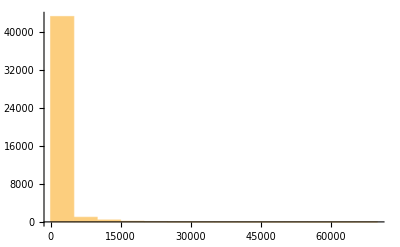

```mathematica
Histogram[Flatten[ImageData[curvature,"Bit16"]]]
```

## sanity checks

```mathematica
HighlightImage[ImageAdjust[orientationNormals[[1]]],{110,101}]
```

```mathematica
HighlightImage[ImageAdjust[orientationNormals[[1]]],{101,110}]
```

```mathematica
MatrixPlot[test,ColorFunction->Function[x,palette[(x+π/2)/π]],ColorFunctionScaling->False]
```

```mathematica
gmVoxels=Position[ImageData[mask],1.]
```

```mathematica
SparseArray[#->1.&/@gmVoxels,Dimensions[ImageData[mask]]]
```

SparseArray[…]

```mathematica
GraphicsRow[{MatrixPlot[ImageData[orientationNormals[[1]]]],MatrixPlot[SparseArray[#->1.&/@gmVoxels,Dimensions[ImageData[mask]]]]}]
```

```mathematica
pmap=Import["/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/data/pmaps-100-microns.tif"]
```

```mathematica
Import/@RandomSample[gmVoxelNames,50]
```

```mathematica
HighlightImage[pmap,{Yellow,{#[[2]],240-#[[1]]}&/@gmVoxels}]
```

```mathematica
GraphicsGrid[Table[Import[coordsToName[{row,i}]],{row,40,65},{i,1,187}],ImageSize->800]
```

```mathematica
Max[Last/@gmVoxels]
```

171

```mathematica
Max[First/@gmVoxels]
```

216

```mathematica
Show[MatrixPlot[ImageData[Import[coordsToName[#]]],ColorFunction->GrayLevel],Graphics[{Yellow,AbsoluteThickness[10],Line[angleToOrientation[getOrientation[#]]]}]]&@gmVoxels[[6]]
```

```mathematica
GraphicsRow[{MatrixPlot[ImageData[orientationNormals[[1]]]],MatrixPlot[SparseArray[#->1.&/@gmVoxels,Dimensions[ImageData[mask]]]]}]
```

MatrixPlot::mat0: Argument SparseArray[Automatic,{239,188,3},0,{1,{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{}},{}}] at position 1 is not a matrix.

Outer Product of vectors, stack them and SVD

```mathematica
MatrixPlot[GaussianFilter[ImageData[orientationNormals[[1]]],3]]
```

```mathematica
GraphicsGrid[Table[Graphics[{Red,Line[angleToOrientation[getOrientation[{row,i}]]]}],{row,50,200},{i,20,180}],ImageSize->800]
```

```mathematica
analyzeOrientation/@testVoxels
```

{{{0.827286,0.172714},0.0110742,{0.604251,0.437954,-1.14955}},{{0.579906,0.420094},0.0093782,{-0.81623,-0.645343,0.922091}},{{0.671894,0.328106},0.0237882,{1.33998,0.766234,-1.20207}},{{0.693851,0.306149},0.0132842,{0.929944,0.678899,-0.972958}},{{0.247276,0.752724},0.0105851,{1.32814,1.16024,-0.399179}},{{0.366253,0.633747},0.0120029,{1.41446,0.915133,-0.67361}},{{0.872856,0.127144},0.00924964,{0.0264119,0.239794,-1.22077}},{{0.775334,0.224666},0.0108855,{0.162549,0.532045,-1.14552}},{{0.509274,0.490726},0.00768002,{0.106081,0.548108,-0.768401}},{{0.191361,0.808639},0.00732808,{-1.04772,-0.995485,0.595018}},{{0.546922,0.453078},0.00592681,{1.00124,0.626054,-0.76848}},{{0.770017,0.229983},0.0100893,{0.0266008,0.357336,-1.10867}},{{0.35197,0.64803},0.00757646,{1.30487,0.892187,-0.586894}},{{0.655946,0.344054},0.01264,{0,-0.581964,1.02972}},{{0.339048,0.660952},0.00613168,{0.536453,0.837537,-0.506643}},{{0.777295,0.222705},0.00882201,{0.0046609,0.364751,-1.10801}},{{0.774612,0.225388},0.00740166,{-0.577557,-0.506603,1.12735}},{{0.59159,0.40841},0.00761421,{0.758716,0.698625,-0.851103}},{{0.699731,0.300269},0.0171472,{0,0.498056,-1.24084}},{{0.50027,0.49973},0.0173979,{1.57035,0.941242,-0.902596}},{{0.668861,0.331139},0.00838788,{0.999143,0.59721,-0.86634}},{{0.495676,0.504324},0.0216253,{1.09733,0.995043,-0.862478}},{{0.616666,0.383334},0.00919817,{0,0.525051,-0.917523}},{{0.451219,0.548781},0.00587487,{0.945926,0.644503,-0.740651}},{{0.487873,0.512127},0.00564903,{-0.261149,-0.701367,0.692883}}}

```mathematica
res=%;
```

```mathematica
#[[1]][[1]]/#[[1]][[2]]&/@res
```

{4.78992,1.38042,2.0478,2.26638,0.328508,0.577917,6.86507,3.45105,1.0378,0.236646,1.20713,3.34816,0.543139,1.90652,0.512969,3.49025,3.43679,1.44852,2.33034,1.00108,2.01988,0.982853,1.60869,0.822222,0.952639}

```mathematica
Mean[First/@(AbsoluteTiming[analyzeOrientation[#]]&/@testVoxels)]
```

2.25261

```mathematica
Length[gmVoxels]*2.25 / 60. /60.
```

8.5575

```mathematica
fitBimodalVonMises/@RandomSample[gmVoxels,10]
```

```mathematica
fitBimodalVonMises[200]
```

-1

```mathematica
o = Flatten[ImageData[GradientOrientationFilter[pimg,sigma]]];
```

```mathematica
w = Flatten[ImageData[GradientFilter[pimg,sigma]]];
```

```mathematica
A = WeightedData[o,w];
```

```mathematica
hist=HistogramDistribution[A,16];
```

```mathematica
Plot[PDF[hist,x],{x,-π/2, π/2},Filling->Axis, PlotRange->All]
```

```mathematica
histPlot=Plot[PDF[hist,x],{x,-π/2, π/2},Filling->Axis, PlotRange->All,Ticks->{Range[-π/2,π/2, π/4]}]
```

```mathematica
Integrate[PDF[hist,x],{x,0.5,1}]
```

0.224339

```mathematica
mse=Total[Table[(PDF[hist,i]-PDF[estDist,i])^2,{i,-π/2,π/2,π/16}]]/16
```

0.0100273

## testing

```mathematica
HOG[img_,nbins_]:=
Module[{mag,ori,mat},
mag=GradientFilter[img,1];
ori=GradientOrientationFilter[img,1,Method->{"UndefinedOrientationValue"->0}];
mat=ImageCooccurrence[{mag,ImageAdjust[ori]},
nbins,{{1}}];
BarChart[Total[mat*Range[0,1-1/nbins,1/nbins]],ChartLabels->Join[{-π/2},Table["",{nbins-2}],{π/2}],Axes->{True,False}]
];
```

```mathematica
HOG[pimg,16]
```

```mathematica
MixtureDistribution
```

```mathematica
d1=Table[RandomVariate[NormalDistribution[-π/4,0.2]],80]
```

{-0.547814,-0.727392,-0.712221,-0.809662,-0.743138,-1.05119,-1.07732,-0.613005,-1.11751,-1.1939,-0.857084,-0.660971,-1.02888,-0.836652,-1.0096,-0.362711,-0.454699,-0.574358,-0.871435,-0.624848,-0.725078,-0.876174,-0.98209,-0.795521,-0.928113,-0.773123,-0.411949,-0.566385,-0.860711,-0.676058,-0.863462,-0.786484,-0.443478,-0.5413,-1.05467,-0.647874,-0.842368,-0.986955,-0.96975,-0.925296,-0.767903,-0.947085,-0.674225,-1.16248,-0.985346,-0.7033,-1.10811,-0.524298,-0.46698,-0.75643,-0.798573,-0.615612,-1.00461,-0.721515,-0.64504,-0.809363,-0.568412,-0.642546,-1.18944,-0.6872,-0.711782,-0.596504,-0.810475,-0.662907,-0.877309,-0.714166,-0.861337,-1.05534,-0.955073,-0.800143,-0.733916,-0.771466,-0.447574,-0.891664,-0.937175,-0.818065,-1.12345,-0.893575,-0.73736,-0.948206}

```mathematica
d2=Table[RandomVariate[NormalDistribution[π/5,0.4]],20]
```

{0.662302,0.980349,0.427463,0.851757,0.610688,0.837155,1.02346,0.741543,0.224833,0.523087,0.387424,0.597167,-0.000894583,0.772252,0.853887,1.13947,0.949945,0.285737,0.812252,1.20961}

```mathematica
data=Join[d1,d2]
```

{-0.547814,-0.727392,-0.712221,-0.809662,-0.743138,-1.05119,-1.07732,-0.613005,-1.11751,-1.1939,-0.857084,-0.660971,-1.02888,-0.836652,-1.0096,-0.362711,-0.454699,-0.574358,-0.871435,-0.624848,-0.725078,-0.876174,-0.98209,-0.795521,-0.928113,-0.773123,-0.411949,-0.566385,-0.860711,-0.676058,-0.863462,-0.786484,-0.443478,-0.5413,-1.05467,-0.647874,-0.842368,-0.986955,-0.96975,-0.925296,-0.767903,-0.947085,-0.674225,-1.16248,-0.985346,-0.7033,-1.10811,-0.524298,-0.46698,-0.75643,-0.798573,-0.615612,-1.00461,-0.721515,-0.64504,-0.809363,-0.568412,-0.642546,-1.18944,-0.6872,-0.711782,-0.596504,-0.810475,-0.662907,-0.877309,-0.714166,-0.861337,-1.05534,-0.955073,-0.800143,-0.733916,-0.771466,-0.447574,-0.891664,-0.937175,-0.818065,-1.12345,-0.893575,-0.73736,-0.948206,0.662302,0.980349,0.427463,0.851757,0.610688,0.837155,1.02346,0.741543,0.224833,0.523087,0.387424,0.597167,-0.000894583,0.772252,0.853887,1.13947,0.949945,0.285737,0.812252,1.20961}

```mathematica
EstimatedDistribution[data,MixtureDistribution[{w1,w2},{VonMisesDistribution[m1,k1],VonMisesDistribution[m2,k2]}]]
```

MixtureDistribution[{0.800083,0.199917},{VonMisesDistribution[-0.795581,27.0451],VonMisesDistribution[0.696655,10.9958]}]

```mathematica
π/4.
```

0.785398

```mathematica
π/5.
```

0.628319

```mathematica
ArrayPlot[Log[Abs[Fourier[ImageData[pimg]]]]]
```

```mathematica
voxels[[1]]
```

/Users/scherf/Dropbox/work/MPI-CBS/orientation-analysis-2D/data/voxels-clj-plugin/test-0-0.tif

```mathematica
test=Import[voxels[[1400]]];
```

```mathematica
test
```

-Graphics-

```mathematica
orientation=GradientOrientationFilter[test,1]//ImageAdjust;
magnitude=GradientFilter[test,1]//ImageAdjust;
ColorCombine[{orientation,magnitude,magnitude},"HSB"]
```

```mathematica
o=Flatten@ImageData@GradientOrientationFilter[test,3];
w=Flatten@ImageData@GradientFilter[test,3];
```

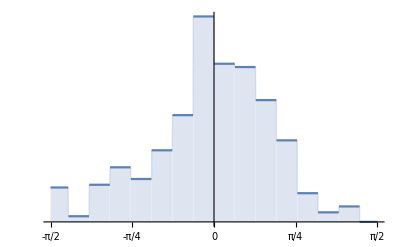

```mathematica
𝒜=WeightedData[o,w];
𝒟=HistogramDistribution[𝒜];
Plot[PDF[𝒟,x],{x,-π/2,π/2},Filling->Axis,PlotRange->All,Ticks->{Range[-π/2,π/2,π/4]}]
```

```mathematica
test
```

-Graphics-

```mathematica
Max@Flatten[ImageData[test]]
```

1.

```mathematica
bin=Binarize[test,0.5]
```

-Graphics-

```mathematica
sk=SkeletonTransform[bin]
```

```mathematica
orientation=GradientOrientationFilter[sk,3]//ImageAdjust;
magnitude=GradientFilter[sk,3]//ImageAdjust;
ColorCombine[{orientation,magnitude,magnitude},"HSB"]
```

```mathematica
o=Flatten@ImageData@GradientOrientationFilter[sk,2];
w=Flatten@ImageData@GradientFilter[sk,2];
```

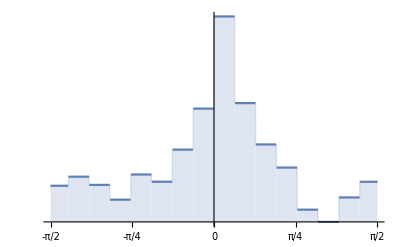

```mathematica
𝒜=WeightedData[o,w];
𝒟=HistogramDistribution[𝒜];
Plot[PDF[𝒟,x],{x,-π/2,π/2},Filling->Axis,PlotRange->All,Ticks->{Range[-π/2,π/2,π/4]}]
```

```mathematica
Show[test,MorphologicalGraph[bin]]
```

-Graphics-

```mathematica
g=MorphologicalGraph[bin];
```

```mathematica
coords=PropertyValue[{g,#},VertexCoordinates]&/@VertexList[g]
```

{{7.5,49.5},{8.5,44.5},{2.5,48.5},{4.5,42.5},{20.5,48.5},{23.5,43.5},{48.5,48.5},{45.5,44.5},{12.5,41.5},{45.5,27.5},{4.5,29.5},{14.5,28.5},{8.5,34.5},{8.5,29.5},{37.5,34.5},{36.5,32.5},{18.5,28.5},{41.5,27.5},{0.5,21.5},{9.5,28.5},{7.5,20.5},{30.5,19.5},{40.5,23.5},{45.5,19.5},{30.5,24.5},{35.5,18.5},{6.5,19.5},{10.5,11.5},{2.5,16.5},{4.5,14.5},{45.5,16.5},{0.5,18.5},{37.5,15.5},{34.5,0.5},{29.5,8.5},{6.5,11.5},{24.5,4.5},{31.5,8.5},{25.5,4.5},{36.5,8.5},{38.5,8.5},{31.5,0.5}}

```mathematica
pmask=Dilation[Image[SparseArray[{Ceiling[50-#[[2]]],Ceiling[#[[1]]]}->1&/@coords,{50,50}]],1]
```

```mathematica
MorphologicalComponents[sk]//Colorize
```

-Graphics-

```mathematica
split=ImageMultiply[sk,ColorNegate[pmask]];
```

```mathematica
MorphologicalComponents[split]//Colorize
```

-Graphics-

```mathematica
HighlightImage[sk,Point/@coords]
```

```mathematica
HighlightImage[test,Point/@coords]
```

```mathematica
edges=EdgeList[g]
```

{1<->5,2<->8,3<->7,4<->6,5<->8,5<->9,6<->7,6<->19,7<->9,8<->13,9<->16,10<->14,11<->12,12<->17,12<->18,13<->14,13<->22,14<->15,15<->16,15<->23,16<->17,17<->25,18<->19,18<->21,19<->26,20<->25,21<->26,21<->28,23<->24,23<->34,24<->29,24<->32,25<->28,26<->30,27<->29,28<->31,29<->32,30<->31,30<->42,31<->35,32<->33,33<->34,33<->39,34<->39,35<->36,35<->40,37<->38,39<->40,40<->41}

```mathematica
Clear[analyzeEdge]
analyzeEdge[v1_<->v2_,coords_,vertices_]:=Module[{vec},
vec=coords[[Position[vertices,v2][[1,1]]]]-coords[[Position[vertices,v1][[1,1]]]];
{ArcTan[vec[[2]]/(vec[[1]]+$MachineEpsilon)],Norm[vec]}]
```

```mathematica
Length[coords]
```

42

```mathematica
Graphics[Point/@coords]
```

```mathematica
g
```

```mathematica
VertexList[g]
```

{1,5,2,8,3,7,4,6,9,19,13,16,10,14,11,12,17,18,22,15,23,25,21,26,20,28,24,34,29,32,30,27,31,42,35,33,39,36,40,37,38,41}

```mathematica
vertices=VertexList[g];
```

```mathematica
lines=Line[{coords[[Position[vertices,#[[1]]][[1,1]]]],coords[[Position[vertices,#[[2]]][[1,1]]]]}]&/@edges;
```

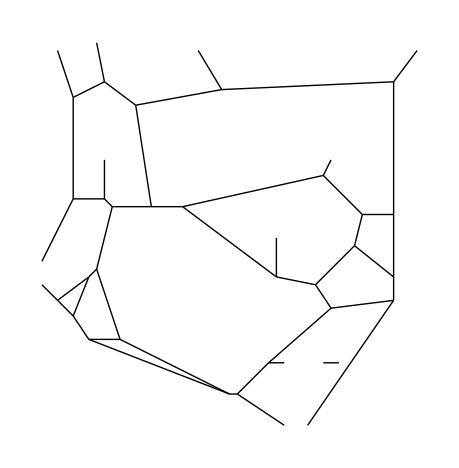

```mathematica
Graphics[lines]
```

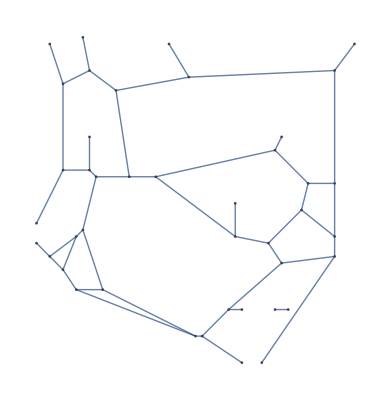

```mathematica
g
```

```mathematica
res=analyzeEdge[#,coords,vertices]&/@edges;
```

```mathematica
test
```

-Graphics-

```mathematica
Histogram[Flatten[ConstantArray[#[[1]],Round[#[[2]]]]&/@res]]
```

```mathematica
Histogram[First/@res,{-π/2,π/2,π/15}]
```

```mathematica
test
```

-Graphics-

```mathematica
𝒜=WeightedData[o,w];
𝒟=HistogramDistribution[𝒜];
Plot[PDF[𝒟,x],{x,-π/2,π/2},Filling->Axis,PlotRange->All,Ticks->{Range[-π/2,π/2,π/4]}]
```

```mathematica
o1=First/@res;
w1=Last/@res;
```

```mathematica
o1
```

{-0.909753,-0.785398,1.10715,0.165149,0.380506,0.,0.463648,1.39094,0.785398,0.260602,1.30454,0.321751,-0.558599,-0.785398,Indeterminate,0.674741,0.179853,-0.643501,0.321751,-0.551655,-0.982794,1.2925,0.785398,-0.463648,0.950547,-0.588003,0.785398,0.,0.,1.4289,0.785398,-0.785398,-1.13839,-0.197396,-0.2783,-0.404892,0.950547,Indeterminate,0.785398,1.10715,-0.2783,0.,-0.982794,0.,-0.463648,0.}

```mathematica
w1
```

{11.4018,4.24264,4.47214,6.08276,5.38516,4.,2.23607,11.1803,2.82843,15.5242,11.4018,6.32456,9.43398,9.89949,2.,6.40312,11.1803,5.,6.32456,15.2643,3.60555,7.28011,9.89949,11.1803,8.60233,7.2111,8.48528,2.,1.,7.07107,2.82843,2.82843,14.3178,5.09902,14.5602,7.61577,8.60233,4.,1.41421,2.23607,7.28011,4.,3.60555,8.,4.47214,2.}

```mathematica
𝒜=WeightedData[o1,w1];
𝒟=HistogramDistribution[𝒜];
Plot[PDF[𝒟,x],{x,-π/2,π/2},Filling->Axis,PlotRange->All,Ticks->{Range[-π/2,π/2,π/4]}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Indeterminate>If[Histogram`HistogramListDump`binwidth$112155≤4.44089×10^-16,Mean[{-1.13839,-0.982794,-0.909753,-0.785398,-0.643501,-0.588003,-0.558599,-0.551655,-0.463648,-0.404892,-0.2783,«7»,0.785398,0.950547,1.10715,1.30454,1.39094,Indeterminate,0.179853,0.674741,1.2925,1.4289}],Histogram`HistogramListDump`binwidth$112155].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

BinLists::bins: The bin specification {Histogram`HistogramListDump`res$112155} is not a list of 2 or 3 real values.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[Histogram`HistogramListDump`res$112155].

BinLists::bins: The bin specification {Histogram`HistogramListDump`res$112155} is not a list of 2 or 3 real values.

General::stop: Further output of BinLists::bins will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[Histogram`HistogramListDump`res$112155].

Last::normal: Nonatomic expression expected at position 1 in Last[Histogram`HistogramListDump`res$112155].

First::normal: Nonatomic expression expected at position 1 in First[Histogram`HistogramListDump`res$112155].

Last::normal: Nonatomic expression expected at position 1 in Last[Histogram`HistogramListDump`res$112155].

First::normal: Nonatomic expression expected at position 1 in First[Histogram`HistogramListDump`res$112155].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[Histogram`HistogramListDump`res$112155].

General::stop: Further output of Last::normal will be suppressed during this calculation.

-Graphics-

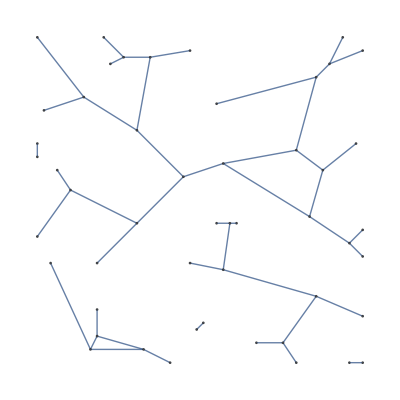

```mathematica
g
```

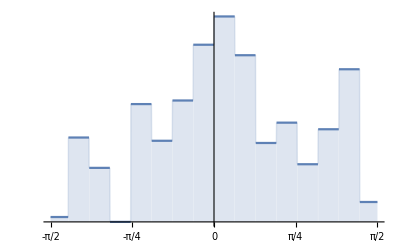

```mathematica
𝒜=WeightedData[o,w];
𝒟=HistogramDistribution[𝒜];
Plot[PDF[𝒟,x],{x,-π/2,π/2},Filling->Axis,PlotRange->All,Ticks->{Range[-π/2,π/2,π/4]}]
```

```mathematica
test
```